```mathematica
freq:=440
bits:=16(*effectively the number of steps*)
μs:=10^-6
step:=N[1/(freq bits)] (*micro-seconds*)
clockrate=N[freq bits];
CLOCKFREQ:=16000000
```

```mathematica
(*v[t_]:=2.5 Sin[2π freq t]+2.5*)
v[t_]:= 8(Sin[2π freq t]+1)
```

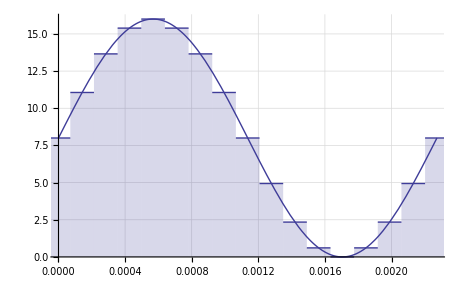

```mathematica
puretone:=Plot[v[t],{t,0,1/freq}]
digitone:=DiscretePlot[v[t],{t,0,1/freq,step},ExtentSize->Full]
Show[{puretone,digitone},GridLines->Automatic]
```

Output from wavegen() on Arduino

```mathematica
data4:={8,11,13,15,15,15,13,11,8,5,3,1,1,1,3,5}
timestep4:=1/8 π{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

data5:={16,19,22,24,27,29,30,31,31,31,30,29,27,24,22,19,16,13,10,8,5,3,2,1,1,1,2,3,5,8,10,13}
timestep5:=1/16 π{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31}
data6:={32,35,38,41,44,47,49,52,54,56,58,60,61,62,63,63,64,63,63,62,61,60,58,56,54,52,49,47,44,41,38,35,32,29,26,23,20,17,15,12,10,8,6,4,3,2,1,1,0,1,1,2,3,4,6,8,10,12,15,17,20,23,26,29}
timestep6:=1/32 π{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}
data7:={64,67,70,73,76,79,82,85,88,91,94,96,99,102,104,106,109,111,113,115,117,118,120,121,123,124,125,126,126,127,127,127,128,127,127,127,126,126,125,124,123,121,120,118,117,115,113,111,109,106,104,102,99,96,94,91,88,85,82,79,76,73,70,67,64,61,58,55,52,49,46,43,40,37,34,32,29,26,24,22,19,17,15,13,11,10,8,7,5,4,3,2,2,1,1,1,0,1,1,1,2,2,3,4,5,7,8,10,11,13,15,17,19,22,24,26,29,32,34,37,40,43,46,49,52,55,58,61}
timestep7:=1/64 π{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127}
data8:={128,131,134,137,140,143,146,149,152,156,159,162,165,168,171,174,176,179,182,185,188,191,193,196,199,201,204,206,209,211,213,216,218,220,222,224,226,228,230,232,234,236,237,239,240,242,243,245,246,247,248,249,250,251,252,252,253,254,254,255,255,255,255,255,256,255,255,255,255,255,254,254,253,252,252,251,250,249,248,247,246,245,243,242,240,239,237,236,234,232,230,228,226,224,222,220,218,216,213,211,209,206,204,201,199,196,193,191,188,185,182,179,176,174,171,168,165,162,159,156,152,149,146,143,140,137,134,131,128,125,122,119,116,113,110,107,104,100,97,94,91,88,85,82,80,77,74,71,68,65,63,60,57,55,52,50,47,45,43,40,38,36,34,32,30,28,26,24,22,20,19,17,16,14,13,11,10,9,8,7,6,5,4,4,3,2,2,1,1,1,1,1,0,1,1,1,1,1,2,2,3,4,4,5,6,7,8,9,10,11,13,14,16,17,19,20,22,24,26,28,30,32,34,36,38,40,43,45,47,50,52,55,57,60,63,65,68,71,74,77,80,82,85,88,91,94,97,100,104,107,110,113,116,119,122,125}
timestep8:=1/128 π{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}
```

```mathematica
bit4:=ListPlot[Thread[{timestep4,16*data4}],PlotStyle->{Black,PointSize[0.01]},Filling->Axis];
```

```mathematica
bit5:=ListPlot[Thread[{timestep5,8*data5}],PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
bit6:=ListPlot[Thread[{timestep6,data6/2}],PlotStyle->{Orange,PointSize[0.01]},Filling->Axis];
bit7:=ListPlot[Thread[{timestep7,2*data7}],PlotStyle->{Yellow,PointSize[0.01]}];
bit8:=ListPlot[Thread[{timestep8,data8}],PlotStyle->{Green,PointSize[0.01]},Filling->Axis];
```

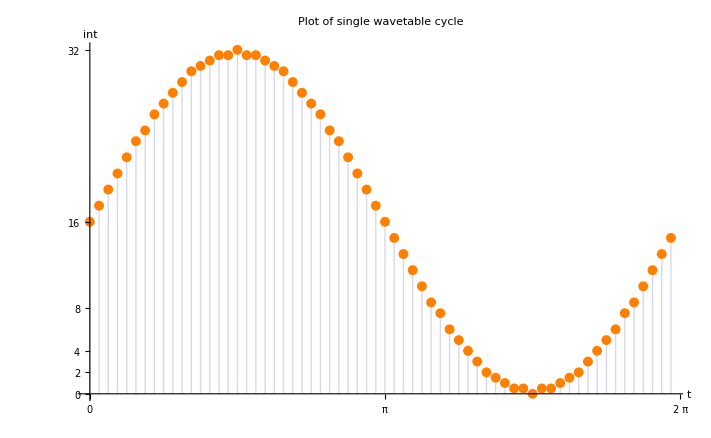

```mathematica
Show[bit6,PlotLabel->"Plot of single wavetable cycle",AxesLabel->{"t","int"},
Ticks->{{0,π,2π},{0,2,4,8,16,32,64,128,256}}
]
```

```mathematica
(*http://www.tonalsoft.com/pub/news/pitch-bend.aspx*)
```

```mathematica
frequency:={
(*OCTAVE -3 *)
32.7031956626,34.6478288721,36.7080959897,38.8908729653,41.2034446141,43.6535289291,46.2493028390,48.9994294977,51.9130871975,55,58.2704701898,61.7354126570,
(*OCTAVE -2 *)
65.4063913251,69.2956577442,73.4161919794,77.7817459305,82.4068892282,87.3070578583,92.4986056779,97.9988589954,103.8261743950,110,
116.5409403795,123.4708253140,
(*OCTAVE -1 *)
130.8127826503,138.5913154884,146.8323839587,155.5634918610,164.8137784564,174.6141157165,184.9972113558,195.9977179909,207.6523487900,220,233.0818807590,246.9416506281,
(*OCTAVE 0 (MIDDLE OCTAVE)*)
261.6255653006,277.1826309769,293.6647679174,311.1269837221,329.6275569129,349.2282314330,369.9944227116,391.9954359817,415.3046975799,440,
466.1637615181,493.8833012561,
(*OCTAVE 1 *)
523.2511306012,554.3652619537,587.3295358348,622.2539674442,659.2551138257,698.4564628660,
739.9888454233,783.9908719635,830.6093951599,880,
932.3275230362,987.7666025122,
(*OCTAVE 2 *)
1046.502261202,1108.730523907,1174.659071670,
1244.507934888,1318.510227652,1396.912925732,
1479.977690847,1567.981743927,1661.218790320,
1760, 1864.655046072,1975.533205025,
(*OCTAVE 3 *)
2093.004522405,2217.461047815,2349.3181433393,
2489.015869777,2637.020455303,2793.825851464,2959.955381693,3135.963487854,3322.437580640,3520,
3729.310092145,3951.066410049
}
```

```mathematica
OCR1A = Round[CLOCKFREQ/(64frequency)]-1
```

{7644,7214,6809,6427,6066,5726,5404,5101,4815,4544,4289,4049,3821,3607,3404,3213,3033,2862,2702,2550,2407,2272,2144,2024,1910,1803,1702,1606,1516,1431,1350,1275,1203,1135,1072,1011,955,901,850,803,757,715,675,637,601,567,535,505,477,450,425,401,378,357,337,318,300,283,267,252,238,224,212,200,189,178,168,158,149,141,133,126,118,112,105,99,94,88,83,79,74,70,66,62}

```mathematica
Round[CLOCKFREQ/(OCR1A*64)]
```

{33,35,37,39,41,44,46,49,52,55,58,62,65,69,73,78,82,87,93,98,104,110,117,124,131,139,147,156,165,175,185,196,208,220,233,247,262,277,294,311,330,350,370,392,416,441,467,495,524,556,588,623,661,700,742,786,833,883,936,992,1050,1116,1179,1250,1323,1404,1488,1582,1678,1773,1880,1984,2119,2232,2381,2525,2660,2841,3012,3165,3378,3571,3788,4032}

## Expected Output: Additive Synthesis

```mathematica
valsquare:={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63,63}
valramp:={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63}
valtri:={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}
squarebit6:=ListLinePlot[Thread[{timestep6,valsquare}]]
rampbit6:=ListLinePlot[Thread[{timestep6,valsquare}]]
sinebit6:=ListLinePlot[Thread[{timestep6,data6}]]
synth1:=valsquare+data6-(valsquare*data6)/32;
synth2:=valramp+data6-(valramp*data6)/32
synth3:=data6+data6-(data6*data6)/32
plotsynth1:=ListLinePlot[Thread[{timestep6,synth1}]]
plotsynth2:=ListLinePlot[Thread[{timestep6,synth2}]]
plotsynth3:=ListLinePlot[Thread[{timestep6,synth3}]]
```

```mathematica
Show[{plotsynth1,plotsynth2,plotsynth3}];
```

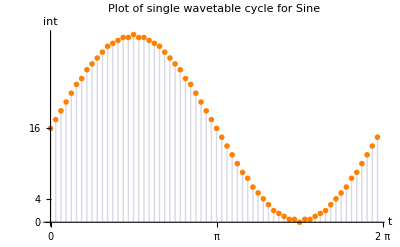

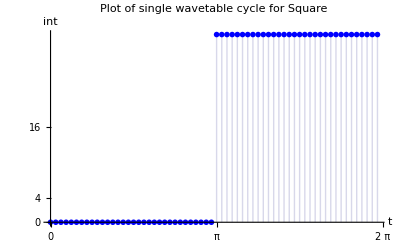

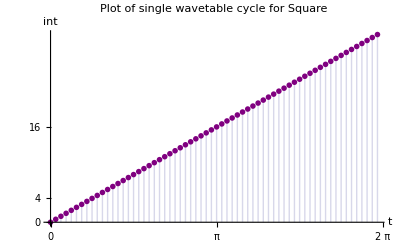

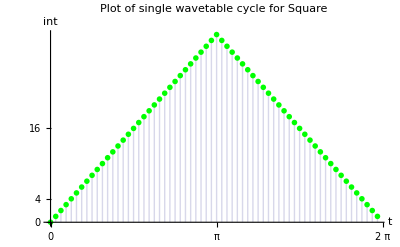

```mathematica
Show[{bit6},PlotLabel->"Plot of single wavetable cycle for Sine",AxesLabel->{"t","int"},
Ticks->{{0,π,2π},{0,2,4,8,16,32,64,128,256}}
]
Show[{ListPlot[Thread[{timestep6,valsquare/2}],PlotStyle->{Blue,PointSize[0.01]},Filling->Axis]},PlotLabel->"Plot of single wavetable cycle for Square",AxesLabel->{"t","int"},
Ticks->{{0,π,2π},{0,2,4,8,16,32,64,128,256}}
]
Show[{ListPlot[Thread[{timestep6,valramp/2}],PlotStyle->{Purple,PointSize[0.01]},Filling->Axis]},PlotLabel->"Plot of single wavetable cycle for Ramp",AxesLabel->{"t","int"},
Ticks->{{0,π,2π},{0,2,4,8,16,32,64,128,256}}
]
Show[{ListPlot[Thread[{timestep6,valtri}],PlotStyle->{Green,PointSize[0.01]},Filling->Axis]},PlotLabel->"Plot of single wavetable cycle for Triangle",AxesLabel->{"t","int"},
Ticks->{{0,π,2π},{0,2,4,8,16,32,64,128,256}}
]
```